# Quartic Interaction

```mathematica
(* R^4 = (2 m^2)/(M g); R is the equilibrium point. m is the magnetic dipole moment, M the mass of the magnet and g gravity. Natural units: Subscript[μ, 0] = (4π)/3*)
```

Potential

```mathematica
V[r_]= r+R^4/(3 r^3)(*-(4 R)/3*)
```

r+R^4/(3 r^3)

```mathematica
V[R](* Minimum of potential Energy *)
```

(4 R)/3

Force/Mg

```mathematica
-D[V[r],r]
```

-1+R^4/r^4

```mathematica
Manipulate[Plot[{r+R^4/(3 r^3)(*-(4 R)/3*),r,R^4/(3 r^3)},{r,0,100},PlotRange-> {0,2 400/3},PlotLegends->{"V_eff","V_Gravitational","V_Magnetic"}, PlotTheme->"Scientific",FrameLabel->{"r","V(r)"}],{{R,50,"R_eq"},0, 100}]
```

Initial conditions,
Energy:

```mathematica
E0=V[2h0]
```

2 h0+R^4/(24 h0^3)

```mathematica
EOM={1/2 r'[t]^2+(V[r]/.r-> r[t])==E0,r[0]==2 h0}
```

{R^4/(3 r[t]^3)+r[t]+1/2 r'[t]^2==2 h0+R^4/(24 h0^3),r[0]==2 h0}

```mathematica
sol=DSolve[EOM,{r[t]},{t}];
```

```mathematica
rsol[t_]=Simplify[(r[t]/.sol[[1]]),{h0>R}]
```

InverseFunction[K[1]^(3/2)/(√((2 h0-K[1]) (-4 h0^2 R^4-2 h0 R^4 K[1]-R^4 K[1]^2+24 h0^3 K[1]^3)))K[1]0#1&][-t/(2 √3 h0^(3/2))+K[1]^(3/2)/(√(48 h0^4 K[1]^3+R^4 K[1]^3-8 h0^3 (R^4+3 K[1]^4)))K[1]02 h0]

```mathematica
Evaluate[rsol[t]/.{h0-> 10,R->1}]
```

InverseFunction[K[1]^(3/2)/(√((2 10-K[1]) (-4 10^2 1^4-2 10 1^4 K[1]-1^4 K[1]^2+24 10^3 K[1]^3)))K[1]0#1&][-t/(20 √30)+K[1]^(3/2)/(√(480001 K[1]^3-8000 (1+3 K[1]^4)))K[1]020]

“Explicit” solution:

```mathematica
∫1/(√(E0-2V[r]))ⅆr
```

∫1/(√(2 h0+R^4/(24 h0^3)-2 (r+R^4/(3 r^3))))ⅆr

```mathematica
Simplify[∫1/(√(E0-2 (r+R^4/(3 r^3))))ⅆr]
```

∫1/(√(2 h0-2 r+R^4/(24 h0^3)-(2 R^4)/(3 r^3)))ⅆr

## Numerically

```mathematica
EOM
```

{R^4/(3 r[t]^3)+r[t]+1/2 r'[t]^2==2 h0+R^4/(24 h0^3),r[0]==2 h0}

Solve the second order equation of motion instead:

```mathematica
EOM2={r''[t]+(D[V[r],r]/.r->r[t])==0,r[0]==2 h0,r'[0]==0}
```

{1-R^4/r[t]^4+r''[t]==0,r[0]==2 h0,r'[0]==0}

```mathematica
DSolve[EOM2,{r[t]},{t}]
```

DSolve::bvimp: General solution contains implicit solutions. In the boundary value problem, these solutions will be ignored, so some of the solutions will be lost.

{}

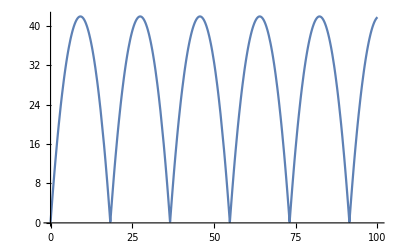

```mathematica
eq=EOM2/.{h0-> n R}/.{R->1,n-> 0.1};
s=NDSolve[eq,{r[t]},{t,0,100}];
Plot[Evaluate[r[t]/.s],{t,0,100},PlotRange->All]
```

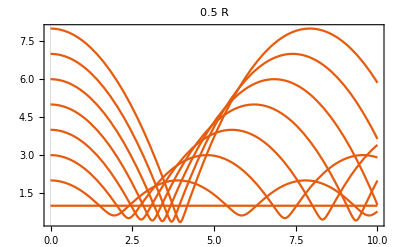

```mathematica
m=Table[
eq=EOM2/.{h0-> n R}/.{R->1};
s=NDSolve[eq,{r[t]},{t,0,10}];
Plot[Evaluate[r[t]/.s],{t,0,10},PlotRange->All, PlotTheme->"Scientific",PlotLabel->n R],{n,0.5,4,0.5}];
Show[m]
```

Plot the results

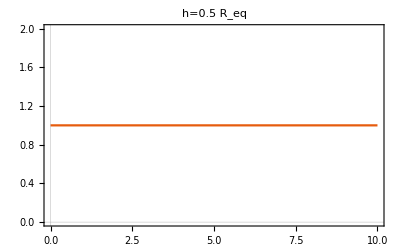
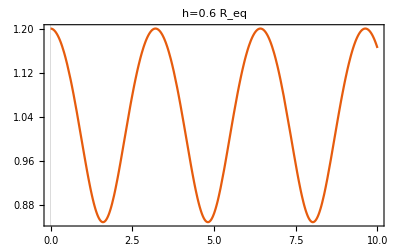
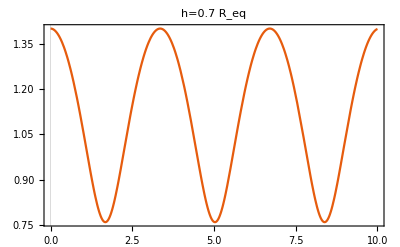
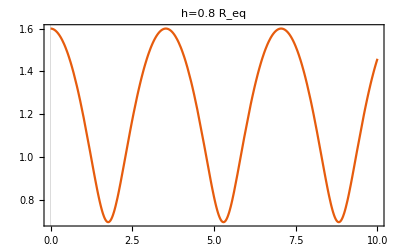
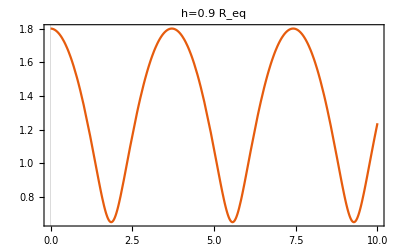
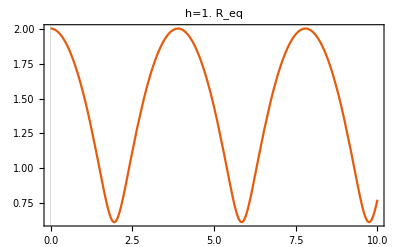
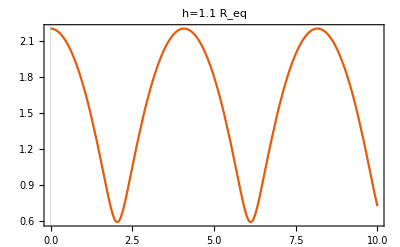
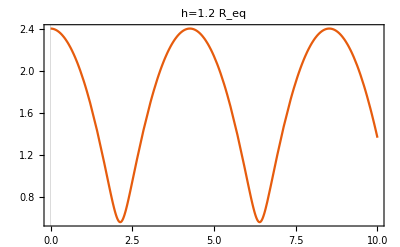

```mathematica
m=Table[
eq=EOM2/.{h0-> n R}/.{R->1};
s=NDSolve[eq,{r[t]},{t,0,10}];
Plot[Evaluate[r[t]/.s],{t,0,10},PlotRange->All, PlotTheme->"Scientific",PlotLabel->"h="<>ToString[n] "R_eq"],{n,0.5,2,0.1}]
```

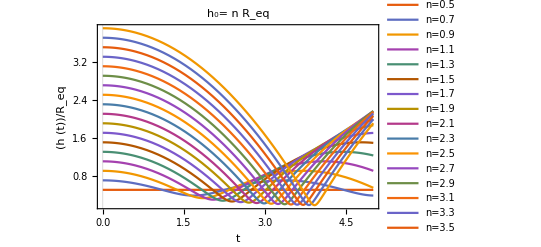

```mathematica
Step=0.2;
nmin=0.5;
nmax=4;
tmax=5;
m2=Table[
eq=EOM2/.{h0-> n R}/.{R->1};
s=NDSolve[eq,{r[t]},{t,0,tmax}]
,{n,nmin,nmax,Step}];
Plot[Evaluate[r[t]/2/.m2],{t,0,tmax},PlotRange->All,FrameLabel->{"t","(h (t))/R_eq"}, PlotTheme->"Scientific",PlotLegends->Table["n="<>ToString[n],{n,nmin,nmax,Step}],PlotLabel->"h_0= n R_eq"]
```

Conclusion: There is minimal approximation in this model. Can it be compared to the experiment?